```mathematica
(*Notebook to compute the BAU from WKB expressions using a top quark source*)
```

### Definitions

```mathematica
(*constants*)
```

```mathematica
GF=1.16638*(10^-5);
v=1/Sqrt[Sqrt[2]*GF];
g2=0.652;
mt=173.34;
yt=√2 mt/v;
```

```mathematica
(*Fiducial values*)
```

```mathematica
Tn=100;
vn=100;
lw=5/Tn;
```

```mathematica
(*Test kink profile functions*)
```

```mathematica
θ[z_]:=ArcTan[vn(1-Tanh[z/lw])/1000];
ϕ[z_]:=vn/2(1+Tanh[z/lw]);
```

```mathematica
m[y_,z_]:=1/(√2)y ϕ[z]
```

```mathematica
(*Plot[{θ[z],D[θ[zp],zp]/.zp->z},{z,-1,1},PlotRange->All]*)
```

### Cline-Kanulainen coefficients from 2001.00568

```mathematica
γw[vw_]:=1/(√(1-vw^2));
```

```mathematica
Q81[vw_,T_]:=(3 (-1+vw^2) (-Log[Abs[-1+vw]]-I Pi+Log[1+vw]))/(4 π^2 T^2);
```

```mathematica
Q82[vw_,T_]:=(3ArcTanh[vw])/(2Pi^2vw γw[vw]^2T^2);
```

```mathematica
(*Plot[{10^5Q82[vw,Tn],10^5Re[Q81[vw,Tn]],10^5Im[Q81[vw,Tn]]},{vw,0,1}]*)
```

```mathematica
Dq[T_]:=7.2/T;
```

```mathematica
Dh[T_]:=20/T;
```

```mathematica
D0=1;
D0h=2;
```

```mathematica
D2[vw_]:=(vw (-1+2 vw^2)+(-1+vw^2)^2 ArcTanh[vw])/vw^3;
D2h[vw_]:=(2 (vw (-1+2 vw^2)+(-1+vw^2)^2 ArcTanh[vw]))/vw^3;
```

```mathematica
Γtot[Dα_,d0_,d2_]:=d2/(d0 Dα);
DWKB[vw_,Dα_,d0_,d2_]:=(d2-vw^2d0)/(d0 Γtot[Dα,d0,d2]);
```

```mathematica
(*Plot[ DWKB[vw,Dq[Tn],D0,D2[vw]],{vw,0,1}]*)
```

### Source

```mathematica
(*Definition from Eq.(37) of 2001.00568*)
```

```mathematica
ddm2dθ[M_,θ_,z_]:=D[M^2 D[θ,zp],{zp,1}]/.zp->z;
```

```mathematica
(*Plot[ddm2dθ[m[yt,zp],θ[zp],z],{z,-0.2,0.2},PlotRange->All]*)
```

```mathematica
S1[h_,vw_,T_,M_,θ_,z_]:=-vw γw[vw]h ddm2dθ[M,θ,z] Q81[vw,T];
```

```mathematica
S2[h_,vw_,T_,M_,θ_,z_]:=-vw γw[vw]h ddm2dθ[M,θ,z] Q82[vw,T];
```

```mathematica
S1p[h_,vw_,T_,M_,θ_,z_]:= D[S1[h,vw,T,M,θ,zp],zp]/.zp->z;
```

```mathematica
S2p[h_,vw_,T_,M_,θ_,z_]:= D[S2[h,vw,T,M,θ,zp],zp]/.zp->z;
```

```mathematica
(*Definition from Eq.(61) of 2001.00568*)
```

```mathematica
SWKB[h_,vw_,T_,M_,θ_,Dα_,d0_,d2_,z_]:=(S1[h,vw,T,M,θ,z]/d0-(vw S1p[h,vw,T,M,θ,z]+S2p[h,vw,T,M,θ,z])/(d0 Γtot[Dα,d0,d2]));
```

```mathematica
(*Plotting norm of SWKB for debugging*)
```

```mathematica
Manipulate[Plot[{(a/(a+b))kT0 Tn^2/6 Norm[SWKB[-1,-vw,Tn,m[yt,zp],θ[zp],Dq[Tn],D0,D2[vw],z]]},{z,-0.2,0.2},PlotStyle->{Red},Frame->True,GridLines->Automatic,PlotLabel->Row@{ "υ_w=",vw""},FrameLabel->{Style["z",FontSize->18,FontFamily->"Times"],Style["|S̄|",FontSize->18,FontFamily->"Times"]},PlotRange->All],{vw,0.1,0.999}]
```

### BAU from Cirigliano et al

```mathematica
(*k factors related to the chemical potential defined as in Eq 72 of hep-ph/0412354 (Lee-Cirigliano-Ramsey-Musolf)*)
kQ30=6.;kT0=3.;kB0=3.;kH0=2.;
a=kH0(9kQ30+9kT0+kB0);
b=9kQ30 kT0+kQ30 kB0+4kT0 kB0;
```

```mathematica
r1=(9kQ30 kT0-5kQ30 kB0-8kT0 kB0)/(a);
r2=kH0 kB0^2(5kQ30+4kT0)(kQ30+2kT0)/(a^2);
```

```mathematica
(*thermal decay widths*)
```

```mathematica
Γmt[T_,m0_]:=((2*kT0))0.79(m0)^2/(T);
Γh[T_,ϕ_]:=((kH0))(g2^2(ϕ)^2)/(4(25)T);(*need to use mW mass z-dependent profile*)
Γss[T_]:=((kT0))8.7*10^(-3)T; 
Γws[T_]:=(2*kT0)6.3*10^(-6)T;
```

```mathematica
(*Effective thermal decay width*)
```

```mathematica
Γbar[T_,m0_,ϕ_]:=(a(Γmt[T,m0]+Γh[T,ϕ]))/(kH0 (a+b));
```

```mathematica
(*Dbar[vw_,T_]:=1/(a+b)(b Dq[T]+a Dh[T]); *)
```

```mathematica
(*Effective diffusion coefficient*)
```

```mathematica
Dbar[vw_,T_]:=1/(a+b)(b DWKB[vw,Dq[T],D0,D2[vw]]+a DWKB[vw,Dh[T],D0h,D2h[vw]]);
```

```mathematica
(*roots of the auxiliary eq of the homogenous case for the diffusion equation*)
```

```mathematica
κp[vw_,T_,m0_,ϕ_]:=(vw+√(vw^2+4Γbar[T,m0,ϕ]Dbar[vw,T]))/(2Dbar[vw,T]);
```

```mathematica
κm[vw_,T_,m0_,ϕ_]:=(vw-√(vw^2+4Γbar[T,m0,ϕ]Dbar[vw,T]))/(2Dbar[vw,T]);
```

```mathematica
(*Amplitude A=A1+A2 of the solution to the diff equation. The (a/(a+b)S0) term below corresponds to the definition of Sbar in Cirigliano et al hep-ph/0412354*)
```

```mathematica
A1[vw_,T_,m0_,ϕ_,S0_,z_]:=(a/(a+b)S0) kT0 T^2/6 Exp[-κp[vw,T,m0,ϕ]z]/(Dbar[vw,T]κp[vw,T,m0,ϕ])
A2[vw_,T_,m0_,ϕ_,S0_,z_]:=(a/(a+b)S0)kT0 T^2/6(κm[vw,T,m0,ϕ]/(vw κp[vw,T,m0,ϕ])+Exp[-vw z/Dbar[vw,T]]/vw )
```

```mathematica
vwf=0.1;
```

```mathematica
zpr=0.1;
```

```mathematica
(*Plot A1 and A2 for debugging purposes*)
```

```mathematica
(*Plot[{Re[A1[vwf,Tn,m[yt,z],ϕ[z],SWKB[-1,-vwf,Tn,m[yt,zp],θ[zp],Dq[Tn],D0,D2[vwf],z],z]],Im[A1[vwf,Tn,m[yt,z],ϕ[z],SWKB[-1,-vwf,Tn,m[yt,zp],θ[zp],Dq[Tn],D0,D2[vwf],z],z]],Re[A2[vwf,Tn,m[yt,z],ϕ[z],SWKB[-1,-vwf,Tn,m[yt,zp],θ[zp],Dq[Tn],D0,D2[vwf],z],z]],Im[A2[vwf,Tn,m[yt,z],ϕ[z],SWKB[-1,-vwf,Tn,m[yt,zp],θ[zp],Dq[Tn],D0,D2[vwf],z],z]]},{z,-0.2,0.2},Frame->True,PlotRange->All]*)
```

```mathematica
(*Total amplitude*)
```

```mathematica
Amplitude[vw_,T_,m0_,ϕ_,S0_,Lw_,z1_]:=NIntegrate[ A1[vw,T,m0,ϕ,S0,z],{z,0,z1}]+NIntegrate[A2[vw,T,m0,ϕ,S0,z],{z,-Lw/2,0}];
```

```mathematica
(*Higgs solution*)
```

```mathematica
Higgs[vw_,T_,m0_,ϕ_,S0_,z_,Lw_,z1_]:=Amplitude[vw,T,m0,ϕ,S0,Lw,z1]Exp[(vw z)/Dbar[vw,T]];
```

```mathematica
(*left-handed density nL*)
```

```mathematica
zfix=0.2;
```

```mathematica
nL[vw_,T_,m0_,ϕ_,S0_,z_,Lw_,z1_]:=-(r1+r2 vw^2/(Γss[T] Dbar[vw,T]) (1-DWKB[vw,Dq[T],D0,D2[vw]]/Dbar[vw,T]))Higgs[vw,T,m0,ϕ,S0,z,Lw,z1];
```

```mathematica
(*-(r1+r2 vw^2/(Γss[T] Dbar[vw,T]) (1-DWKB[vw,Dq[T],D0,D2[vw]]/Dbar[vw,T]))/.vw->0.1/.T->100*)
```

```mathematica
Re[nL[vwf,Tn,m[yt,z],ϕ[z],SWKB[-1,-vwf,Tn,m[yt,zp],θ[zp],Dq[Tn],D0,D2[vwf],z],z,0.4,zfix]]
```

Re[(0.328949-0.13761 ⅈ) ⅇ^(0.80502 z)]

```mathematica
(*Plot nL - debugging -*)
```

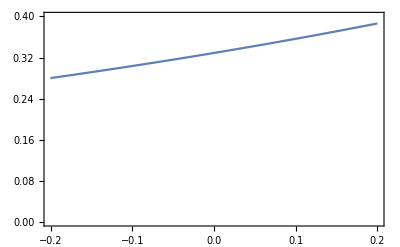

```mathematica
Plot[{Re[(0.32894-0.1376 ⅈ) ⅇ^(0.805 z)]},{z,-zfix,zfix},Frame->True,PlotRange->{0,0.4}]
```

```mathematica
αp[vw_,T_]:=(vw+√(4DWKB[vw,Dq[T],D0,D2[vw]]Γws[T](15/4)+vw^2))/(2DWKB[vw,Dq[T],D0,D2[vw]]);
```

```mathematica
αm[vw_,T_]:=(vw-√(4DWKB[vw,Dq[T],D0,D2[vw]]Γws[T](15/4)+vw^2))/(2DWKB[vw,Dq[T],D0,D2[vw]]);
```

```mathematica
Integrand[vw_,T_,m0_,ϕ_,S0_,z_,Lw_,z1_]:=nL[vw,T,m0,ϕ,S0,z,Lw,z1]*Exp[-αm[vw,T]z];
```

```mathematica
gstar=106.75;
```

```mathematica
gstar2HDM=110.75;(*# degress of freedom in the 2HDM*)
```

```mathematica
se[T_]:=(2Pi^2/45)gstar2HDM T^3;(*density entropy at temperature T*)
```

```mathematica
YB[vw_,T_,m0_,ϕ_,S0_,Lw_]:=(-3 Γws[T])/(2se[T] DWKB[vw,Dq[T],D0,D2[vw]] γw[vw]αp[vw,T])NIntegrate[Integrand[vw,T,m0,ϕ,S0,z,Lw,∞],{z,-∞,-Lw/2}]
```

```mathematica
YBobs=8.59*10^-11;(*Planck collaboration central value*)
```

```mathematica
YB[0.3,Tn,m[1,z],ϕ[z],0.06,lw]
```

3.78793×10^-11

### Control plot

```mathematica
(*ηBg[vw,T,m0,ϕ,S0,Lw]*)
```

```mathematica
(*Re[SWKB[-1,vw,Tn,m[yt,zp],θ[zp],Dq[Tn],D0,D2[vw],z]]*)
```

```mathematica
(*m[yt,z]*)
```

```mathematica
Manipulate[{Abs[YB[vw,Tn,m[yt,z],ϕ[z],SWKB[-1,-vw,Tn,m[yt,zp],θ[zp],Dq[Tn],D0,D2[vw],z],Lw]]/YBobs,Abs[Im[YB[vw,Tn,m[yt,z],ϕ[z],SWKB[-1,-vw,Tn,m[yt,zp],θ[zp],Dq[Tn],D0,D2[vw],z],Lw]]]/YBobs},{vw,0.05,0.999},{Tn,100,200},{Lw,lw,20/Tn}]
```

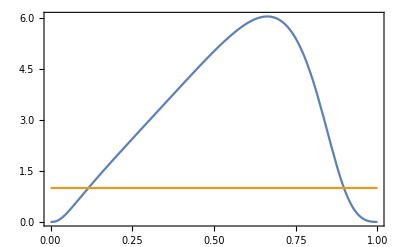

```mathematica
Plot[{Abs[YB[vw,Tn,m[yt,z],ϕ[z],SWKB[-1,-vw,Tn,m[yt,zp],θ[zp],Dq[Tn],D0,D2[vw],z],lw]]/YBobs,1},{vw,0,1},Frame->True]
```